```mathematica
DirectoryStack[]
```

{/Users/claytonho/Documents/Research/Mathematica/Bakeout,/Users/claytonho}

```mathematica
SetDirectory["/Users/claytonho/Documents/Research/Mathematica/Bakeout"]
```

/Users/claytonho/Documents/Research/Mathematica/Bakeout

```mathematica
reshape[file_]:=ArrayReshape[file,{Length[file]/2,2}];
reformat[file_,const_:0]:=Module[
{pressArr=Flatten[file[[2;;;;2]]],
timeArrTxt=ToExpression[StringSplit[#,":"]]&/@Flatten[file[[1;;;;2]]],
timeArrNum},
timeArrNum=N[(#[[1]]+#[[2]]/60+const)]&/@timeArrTxt;
Transpose[{timeArrNum,pressArr}]
];
day=24;
```

```mathematica
d20=reformat[Import["12_20.csv"]];
d21=reformat[Import["12_21.csv"],1*day];
d22=reformat[Import["12_22.csv"],2*day];
d23=reformat[Import["12_23.csv"],3*day];
d26=reformat[Import["12_26.csv"],6*day];
```

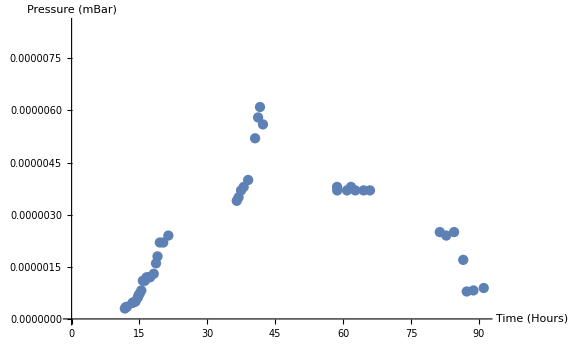

```mathematica
ListPlot[Join[d20,d21,d22,d23],ImageSize->Large,AxesLabel->{"Time (Hours)","Pressure (mBar)"}]
```

```mathematica
d26=reformat[Import["12_26.csv"],0*day];
d27=reformat[{{"00:10"},{8.2*^-7},{"09:56"},{7.3*^-7},{"10:39"},{2.5*^-7}},1*day];
d28=reformat[{{"09:50"},{2.9*^-7},{"10:11"},{1.8*^-7},{"12:30"},{3*^-7},{"20:00"},{3*^-7}},2*day];
d29=reformat[{{"10:00"},{1.6*^-7},{"14:07"},{1.6*^-7},{"14:18"},{1.6*^-7},{"14:34"},{1.6*^-7},{"15:22"},{1.6*^-7},{"15:53"},{1.6*^-7}},3*day];
```

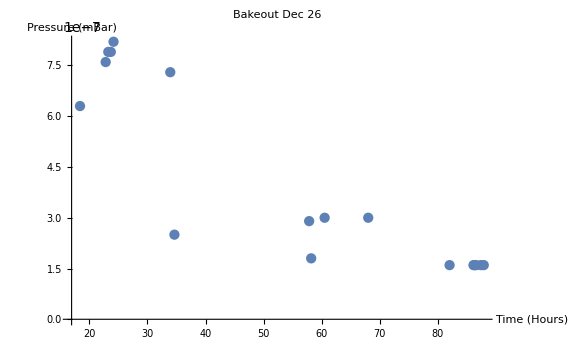

```mathematica
ListPlot[Join[d26,d27,d28,d29],ImageSize->Large,AxesLabel->{"Time (Hours)","Pressure (mBar)"},PlotRange->Full,PlotLabel->"Bakeout Dec 26"]
```

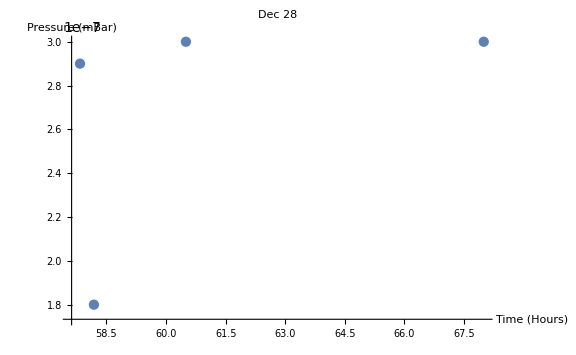

```mathematica
ListPlot[d28,ImageSize->Large,AxesLabel->{"Time (Hours)","Pressure (mBar)"}(*,PlotRange->{3*^-6,5*^-6}*),PlotRange->Full,PlotLabel->"Dec 28"]
```